```mathematica
<< "~gam/MATH/init.m"
```

SetDirectory::cdir: Cannot set current directory to "/nethome/mercier/MATH".

Get::noopen: Cannot open "cosmo.m".

Get::noopen: Cannot open "astro.m".

Get::noopen: Cannot open "math.m".

General::stop: Further output of Get :: noopen will be suppressed during this calculation.

```mathematica
<< "~gam/MATH/cosmo.m"
```

```mathematica
X1d=X/.FindRoot[X/sbrNFW[X]sbrNFW'[X]+1,{X,1}]
```

0.612871

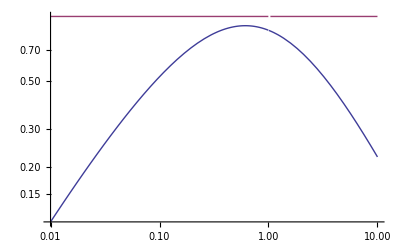

```mathematica
LogLogPlot[{X sbrNFW[X],1},{X,0.01,10}]
```

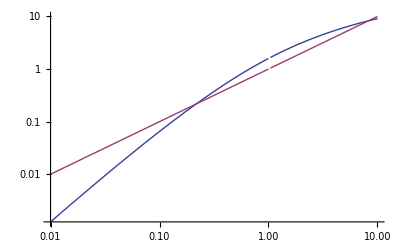

```mathematica
LogLogPlot[{MprojNFW[X],X},{X,0.01,10}]
```

```mathematica
X1=X/.FindRoot[X/MprojNFW[X]MprojNFW'[X]-1,{X,0.9}]
```

1.3182

```mathematica
Fmaj[X_]=X/X1 MprojNFW[X1]
```

1.60776 X

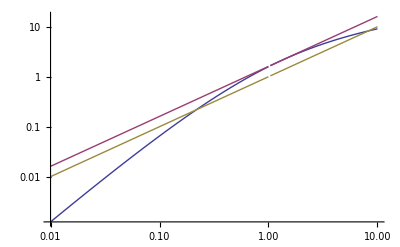

```mathematica
LogLogPlot[{MprojNFW[X],Fmaj[X],X},{X,0.01,10}]
```

```mathematica
Xm=10
```

10

```mathematica
X1=Xm RandomReal[1,10000];
```

```mathematica
q2=RandomReal[1,10000];
```

```mathematica
tab=Transpose[{X1,q2}];
```

```mathematica
X=Select[tab,#[[2]]<2 1000/10000 Xm/MprojNFW[Xm]#[[1]]sbrNFW[#[[1]]]&][[All,1]]
```

{1.17622,1.61505,6.54697,7.29756,7.1488,2.29842,0.372336,4.0633,0.382043,2.88848,2.23059,9.43476,0.92653,0.439794,3.98673,0.161523,0.799659,6.82434,2.88423,5.0525,5.11537,0.508742,1.72818,8.08978,7.75315,3.56239,3.58266,2.1006,3.33645,1.30831,6.62671,5.92746,3.75293,0.158621,6.7565,2.14955,2.3782,1.2349,7.45298,0.488096,0.64527,9.96328,4.82084,6.91761,8.58187,7.5244,4.36441,1.79177,6.68256,7.46006,0.38152,1.2712,7.61079,0.598809,9.36228,1.12324,3.94125,0.611264,0.553251,4.63029,0.459194,1.61927,1.80806,1.67718,2.38154,5.69657,5.94181,1.73629,8.26738,5.81306,2.66211,6.11553,2.95364,1.90435,1.55172,1.06405,0.430235,3.57417,6.65457,5.5621,3.43725,6.95998,2.38737,9.24046,1.36095,2.23075,1.93668,7.83586,0.961786,0.297012,3.92224,2.50453,1.69024,7.82827,1.31135,3.64812,3.53018,1.64066,2.91672,1.77486,6.35593,5.78266,2.89352,2.98853,0.699891,5.31199,5.67297,1.45631,0.455098,9.07591,0.30726,3.90876,1.93107,7.5,2.18439,2.74736,5.77354,2.33612,4.39107,3.07741,7.46119,0.747858,1.20829,1.92029,3.3626,1.86828,0.69399,0.699385,7.82108,9.78414,2.94956,0.852848,2.72059,4.90862,2.00119,2.11256,0.609858,3.22573,0.426152,0.169959,4.41126,3.9555,1.40555,2.57025,1.40715,0.242284,6.70786,2.53567,0.89881,3.03779,2.10371,0.346384,1.42122,2.30079,0.526545,5.36828,2.3796,6.2135,1.5461,7.43026,1.15317,6.25989,0.492854,1.10479,6.93783,1.68302,5.1923,1.62633,0.420146,1.11802,1.9774,1.08398,5.31328,4.49317,5.27746,5.23043,3.03336,4.93721,7.08439,7.81235,4.67305,8.05049,0.41832,0.6318,5.78855,1.73072,1.05212,7.60287,4.01146,7.49615,0.419438,1.96294,4.03257,4.6752,1.77455,6.4908,2.27971,5.04319,6.1574,3.87101,6.54245,1.4275,1.82241,0.959422,3.28322,7.97011,0.429081,0.481327,0.454104,2.32302,9.23512,6.65348,2.6844,3.76273,9.12812,1.53747,4.0081,0.858067,1.45562,3.09196,6.86085,3.91377,2.07336,1.64966,9.83278,2.83938,7.05367,2.31689,0.509909,2.91444,1.1867,3.32032,8.7558,5.21549,5.47017,8.57077,2.23926,6.53554,0.344004,1.41166,2.2434,1.9549,3.49998,2.73558,7.3287,5.74483,0.309715,0.93237,4.35544,5.20632,0.995775,1.16557,9.08093,2.35028,1.9024,1.15495,1.97305,5.26528,2.59671,9.60351,0.641768,6.74958,8.68541,3.44712,0.433616,3.02662,0.657451,2.20032,0.131131,5.88533,1.8924,1.25586,5.12727,0.469711,3.15286,7.00732,1.23834,3.11678,2.24199,8.82848,1.14358,5.38632,0.0245581,3.92389,0.787291,0.647232,7.08839,1.87349,1.38837,1.38848,0.404052,2.1151,3.6679,8.81161,1.55594,2.55369,2.18819,5.30648,3.14444,2.02211,0.70764,6.76138,1.20237,7.91124,5.24878,0.425801,0.148508,1.05326,0.532065,5.19657,0.805187,2.09158,4.62324,7.06903,0.779541,6.63416,8.40541,1.20825,8.33148,4.04067,2.62962,2.9035,8.1829,0.380762,1.76167,7.17945,1.71457,9.51608,1.49921,8.28782,4.25431,4.11886,0.38144,0.79835,0.917246,3.87921,0.487522,7.8283,2.4196,0.909264,1.49933,3.8316,0.95179,8.22715,1.23661,3.32894,8.13989,2.28146,2.15354,6.03694,1.00887,5.92182,8.82845,3.96096,6.05311,4.69829,1.21071,7.89943,2.21865,7.43155,4.4848,5.77983,7.54558,4.929,0.894549,2.18163,0.558748,4.76527,0.904829,6.87606,0.449787,9.84136,3.29207,2.76475,1.38529,2.2227,5.2018,2.71567,4.10945,2.06653,5.16081,5.41071,1.40972,1.47098,4.42157,9.93079,2.60301,8.60097,0.434978,4.50094,2.03237,2.09275,7.73121,5.29177,0.479246,7.34265,8.1292,0.230698,1.12045,0.778574,1.50336,2.82325,3.32338,0.363845,6.5084,9.95506,2.14943,0.402769,0.549639,0.730332,6.90715,3.30498,1.7107,8.04697,2.26356,3.61832,2.74756,1.15056,5.80299,3.13961,3.19732,3.63234,7.48384,6.97236,5.47251,8.72914,0.452825,2.81359,0.320564,4.4202,8.76908,0.237431,2.43243,1.52238,3.0241,7.97799,2.59594,1.08157,8.22937,4.46464,6.0758,1.1568,6.08885,2.4868,7.91947,0.407676,6.49324,2.24566,0.382436,0.228683,5.14016,1.73923,5.3047,7.59914,1.79753,8.52361,8.92967,4.3998,3.29585,1.13683,0.0472518,0.460908,2.13059,7.20554,4.36764,8.66143,0.0567896,4.59706,8.84966,4.82727,3.35934,1.10933,1.77839,5.08235,5.73594,3.1971,1.49069,7.28823,1.10074,1.0452,0.0522349,0.514379,0.638773,5.71425,4.5302,7.20704,5.07174,5.93745,0.365253,2.28216,1.2409,1.5542,2.18778,7.4362,5.64346,1.25934,4.83215,7.15821,0.587343,9.69093,9.19503,7.20804,7.31944,0.150322,8.20284,1.07393,0.712923,0.332497,1.52092,0.73813,0.374262,0.734544,0.263072,3.25879,4.3776,5.84924,4.38071,8.07031,4.45902,8.67403,8.79522,6.09634,8.41484,8.10902,9.82795,5.1191,8.85734,2.19076,3.06818,3.3573,9.0248,1.5695,3.57225,3.8474,1.74375,1.06169,4.48134,6.62899,4.42962,8.49138,1.15901,9.43493,6.66103,6.38474,3.64445,4.55889,9.05717,9.27668,7.6266,2.81921,5.38918,5.63813,0.899522,5.36917,2.5809,1.25646,2.93606,0.0901428,0.239481,3.3527,1.32106,1.75635,7.59902,0.333586,8.36427,5.79842,2.10663,1.76871,0.640838,2.15759,3.50792,1.43004,8.80608,1.10401,7.52905,7.99775,4.26844,4.09787,5.46419,1.85753,0.566218,7.38668,3.80648,5.01687,2.08521,6.08332,2.62592,3.05623,1.33472,3.31821,0.696255,4.08256,3.0467,7.6815,2.93264,0.833093,0.867054,1.50081,6.63845,5.95354,8.55347,1.88253,3.13065,1.29184,6.1219,2.32584,5.59999,3.71556,4.88633,2.81713,5.63316,9.22706,3.98689,1.01456,1.05153,0.893613,0.867487,8.80913,1.19753,3.64672,0.666395,3.60751,6.05661,5.60067,3.58569,1.8529,1.82018,3.50732,7.38117,4.33549,3.62802,1.13327,7.25185,3.92293,7.35403,2.56984,0.989395,2.0071,8.85281,5.00309,7.15664,4.22169,9.33064,5.51345,5.05262,3.51137,9.52309,0.680636,2.24209,5.16704,1.51365,0.54478,2.17406,0.455233,8.42594,0.889388,4.35481,5.48607,0.79838,1.97767,0.393485,0.856638,0.729636,5.94069,0.0363452,5.69203,1.0979,2.31762,0.490945,9.78825,7.30941,5.67371,7.50116,5.25401,2.34837,7.85282,2.22792,8.96536,0.812298,2.23641,1.62199,2.23103,3.88846,0.689191,9.03694,8.52652,1.79672,0.526314,5.1042,1.28589,0.214966,1.43128,7.99735,2.40094,5.29837,5.18222,3.07102,0.420199,8.70787,9.67063,1.99482,8.69872,1.62116,1.94594,0.88222,0.359024,8.2541,1.14592,7.10355,2.58356,0.562875,7.66078,7.14216,7.17888,1.95061,8.2872,0.565328,2.21348,8.98303,2.70106,4.33363,7.63725,2.13644,1.02272,0.804429,1.27182,5.05311,1.91921,0.897132,0.993381,0.366846,1.8279,2.74246,0.526439,1.75349,6.50185,2.49909,2.16545,2.79067,5.6199,8.35359,3.20389,3.58818,8.86424,0.567203,6.30899,6.45567,0.414764,0.812179,8.0669,3.45032,4.11194,9.60578,0.930378,4.53266,9.25188,7.555,1.50775,9.50116,3.44235,0.391676,1.159,6.39187,2.33928,5.33001,7.50172,6.90677,1.73383,8.64456,1.20077,2.18976,1.79064,5.25026,1.52054,0.940065,1.41674,6.1273,3.72597,5.48327,4.55556,3.00661,9.34984,1.4782,7.77079,3.56741,3.81436,3.84326,4.33568,6.01491,3.45768,2.45342,1.61266,1.98371,7.44283,1.51092,5.70491,2.5533,5.58789,2.89892,3.68026,2.14763,0.57533,1.31258,9.53312,5.89425,2.40312,3.06955,0.353072,0.660707,4.38979,4.89057,3.23318,4.96897,2.02101,2.14595,2.74627,0.299846,0.131,4.89468,4.17408,1.57123,0.392155,1.40361,5.14849,2.89773,0.226132,5.4889,1.77463,0.843246,9.12623,1.48605,6.32018,1.67585,6.17283,6.90068,6.24485,9.08513,2.4551,7.16427,0.735616,1.94466,1.7904,0.620197,0.597411,2.09004,2.23982,0.569269,0.279348,1.15105,5.10151,7.94825,0.249981,1.96148,6.09367,0.435987,4.23396,4.69049,3.29094,4.01211,0.222421,8.56486,2.37687,2.84474,5.96259,2.50956,0.347134,5.03223,5.80892,6.86509,0.409418,4.21776,3.3284,1.51825,6.5724,9.8251,5.47009,0.586424,9.35423,0.756271,3.28426,3.8918,0.785364,1.8369,0.288225,4.37672,0.404385,0.459454,4.78506,0.809881,7.41293,8.12024,4.34907,7.239,1.28692,7.0443,8.13407,3.68196,3.62003,7.16014,9.20453,7.43343,3.27005,2.2402,4.58435,9.9582,0.211609,9.56365,0.568089,2.16888,4.44552,4.67031,7.10058,8.21496,2.4364,7.14307,3.67959,8.99199,0.504571,4.07849,0.401455,0.874081,5.38606,2.60244,1.6755,0.613161,0.320104,7.5138,7.67494,4.37518,3.88879,5.43023,3.72749,2.95469,4.36471,1.58741,0.592028,2.12449,6.12402,1.51452,4.3327,4.50754,7.06503,1.42058,5.2394,5.9489,2.50292,6.96187,8.77759,0.386226,4.47427,2.63097,2.01612,7.05685,5.56627,4.51868,4.89186,3.8503,2.10118,1.76086,2.19389,8.29302,2.03193,6.90178,2.22141,4.53504,4.58189,4.71542,1.73773,1.99504,1.00562,1.63518,1.03547,0.890139,2.51023,3.70531,0.247801,6.54584,0.380105,1.37331,2.02541,9.85108,1.8079,1.39359,0.660172,9.81288,2.95711,4.11818,9.67437,6.86525,7.42347,0.92017,3.67671,4.75671,9.85267,6.80143,5.37185,3.92321,3.30413,2.81077,0.270547,4.24822,5.18431,1.42089,2.85068,0.258958,7.13142}

```mathematica
Length[X]
```

1006

```mathematica
lX = Log10[X];
```

```mathematica
lXbins = Range[-1.95,0.95,0.1]
```

{-1.95,-1.85,-1.75,-1.65,-1.55,-1.45,-1.35,-1.25,-1.15,-1.05,-0.95,-0.85,-0.75,-0.65,-0.55,-0.45,-0.35,-0.25,-0.15,-0.05,0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95}

```mathematica
cts = BinCounts[lX,{-2,1,.1}]
```

{0,0,0,1,0,1,1,2,0,1,0,4,3,11,9,24,34,28,29,38,48,54,68,88,66,80,84,109,116,107}

```mathematica
lXbinsplus=lXbins+0.05
```

{-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,1.80411×10^-16,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
lXbinsminus=lXbins-0.05
```

{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,4.16334×10^-17,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}

```mathematica
area = Pi (10^(2lXbinsplus)-10^(2lXbinsminus))
```

{0.00018375,0.000291224,0.000461558,0.00073152,0.00115938,0.0018375,0.00291224,0.00461558,0.0073152,0.0115938,0.018375,0.0291224,0.0461558,0.073152,0.115938,0.18375,0.291224,0.461558,0.73152,1.15938,1.8375,2.91224,4.61558,7.3152,11.5938,18.375,29.1224,46.1558,73.152,115.938}

```mathematica
sdens = cts/area
```

{0.,0.,0.,1367.02,0.,544.219,343.379,433.315,0.,86.2529,0.,137.352,64.9972,150.372,77.6276,130.613,116.749,60.6641,39.6435,32.7761,26.1225,18.5425,14.7327,12.0297,5.69269,4.35375,2.88438,2.36157,1.58574,0.922906}

```mathematica
esdens=Sqrt[cts]/area
```

{0.,0.,0.,1367.02,0.,544.219,343.379,306.4,0.,86.2529,0.,68.6758,37.5262,45.3388,25.8759,26.6612,20.0223,11.4644,7.36161,5.31698,3.77046,2.52331,1.7866,1.28237,0.700722,0.486764,0.314712,0.226197,0.147232,0.0892207}

```mathematica
tabdata=Transpose[{10^lXbins,sdens}]
```

{{0.0112202,0.},{0.0141254,0.},{0.0177828,0.},{0.0223872,1367.02},{0.0281838,0.},{0.0354813,544.219},{0.0446684,343.379},{0.0562341,433.315},{0.0707946,0.},{0.0891251,86.2529},{0.112202,0.},{0.141254,137.352},{0.177828,64.9972},{0.223872,150.372},{0.281838,77.6276},{0.354813,130.613},{0.446684,116.749},{0.562341,60.6641},{0.707946,39.6435},{0.891251,32.7761},{1.12202,26.1225},{1.41254,18.5425},{1.77828,14.7327},{2.23872,12.0297},{2.81838,5.69269},{3.54813,4.35375},{4.46684,2.88438},{5.62341,2.36157},{7.07946,1.58574},{8.91251,0.922906}}

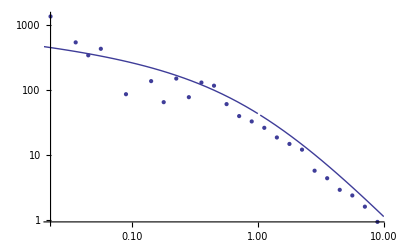

```mathematica
Show[ListLogLogPlot[tabdata],LogLogPlot[50 sbrNFW[Y],{Y,0.01,10}]]
```

```mathematica
tabSelect=Select[tab,#[[2]]<2 1000/10000 Xm/MprojNFW[Xm]X sbrNFW[#[[1]]]&]
```

{}

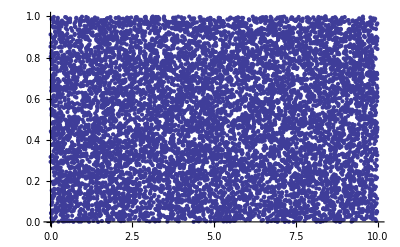

```mathematica
Show[ListPlot[tab],Plot[ 1000/10000 Xm/MprojNFW[Xm]X sbrNFW[]
```